La funzione da calcolare è:

x^2

Calcola lo studio di funzione

----------------------------------------------------------------------------------------

I contenuti sotto radice pari

{}

devono essere maggiori di zero:

{}

I contenuti sotto logaritmi

{}

devono essere maggiori di zero:

{}

Il denominatore:

{1}

deve essere diverso di zero, quindi calcolo i valori per cui il denominatore è minore di zero e maggiore di zero e risulta:

{False,True}

quindi facendo l'intersezione tra questi domini, il dominio è:

True

----------------------------------------------------------------------------------------

La funzione è pari.

La funzione non è dispari.

----------------------------------------------------------------------------------------

Per scoprire dove interseca l'asse x poniamo il numeratore = 0:

x^2==0

che risulta:

x==0

Per scoprire dove interseca l'asse y, calcoliamo f(x) con x=0 se il dominio lo ammette e otteniamo che interseca l'asse y in

y==0

----------------------------------------------------------------------------------------

La funzione è positiva per x<0||x>0

----------------------------------------------------------------------------------------

Gli estremi inferiori per il calcolo del limite sono:

{}

e gli estremi superiori sono:

{}

----------------------------------------------------------------------------------------

La derivata prima della funzione è:

2 x

Le soluzioni della derivata prima sono:

{x→0}

Gli intervalli in cui la derivata è positiva sono:

x>0.

Gli intervalli in cui la derivata è negativa sono:

x<0.

Il grafico della derivata prima è il seguente:

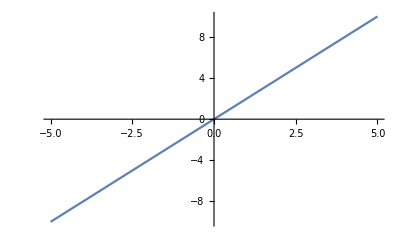

----------------------------------------------------------------------------------------

La derivata seconda è

2

Non ci sono soluzioni per la derivata prima.

La funzione è convessa

Il grafico della derivata seconda è il seguente:

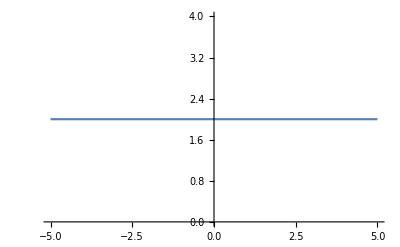

----------------------------------------------------------------------------------------

Il grafico della funzione è:

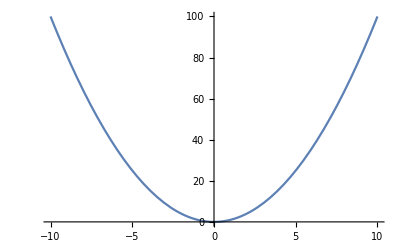

```mathematica
$IterationLimit=$RecursionLimit=50;

Get["Desktop/Progetto Matematica Computazionale/studiofunzioni.m"]

InputField[Dynamic[funzione]]
Dynamic[funzione]
Button["Calcola lo studio di funzione", FrontEndExecute[FrontEndToken[InputNotebook[],"EvaluateNotebook"]]]
Print["La funzione da calcolare è: "]
f[x_]:=Evaluate[funzione];
f[x]
(*(E^x-1)/x
x^3 
(E^x-1)/x
x-Sqrt[x^2-1]
(Sqrt[3]-2*x-Log[35])/(2*x)
(2*x-1)/(x*E^x)
(x*(x-1)^2)/(x+1)^2
x/(E^x-1)
x^2/2-x+Log[x+1]
*)

Print["----------------------------------------------------------------------------------------"];

CalcolaDominio[f,x]

Print["----------------------------------------------------------------------------------------"];

ControlloPariDispari[f,x]

Print["----------------------------------------------------------------------------------------"];

ControlloIntersezioneAssi[f,x]

Print["----------------------------------------------------------------------------------------"];

SegnoFunzione[f,x]

Print["----------------------------------------------------------------------------------------"];

CalcolaLimiti[f,x]

Print["----------------------------------------------------------------------------------------"];

SegnoDerivataPrima[f,x]

Print["----------------------------------------------------------------------------------------"];

SegnoDerivataSeconda[f,x]

Print["----------------------------------------------------------------------------------------"];

GraficoFunzione[f,x]
```